## Modules

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=Module[{hatq, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
For[kk=9, kk≤14, kk++,
Print[kk];
SeedRandom[123456];
data = 
Import[NotebookDirectory[] <> "../processed_data/future_brr_v4/train/" <> ToString[kk] <> ".csv"];
rbtc=data⟦2;;All,5⟧;
rbrr=data⟦2;;All,6⟧;
Print["Calibration..."];
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,5;;6⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
]
```

9

Calibration...

10

Calibration...

11

Calibration...

12

Calibration...

13

Calibration...

14

Calibration...

```mathematica
For[kk=0, kk≤14, kk++,
Print[kk];
data = 
Import[NotebookDirectory[] <> "../processed_data/future_brr_v4/train/" <> ToString[kk] <> ".csv"];
data2= Import[NotebookDirectory[] <> "../processed_data/future_brr_v4/test/" <> ToString[kk] <> ".csv"];
rbtc=data⟦2;;All,5⟧;
rbrr=data⟦2;;All,6⟧;
{α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp[[;;,1]];
vsim=utmp[[;;,2]];
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", h];
he=HedgeEffectiveness[h[[1;;6]]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,6⟧;
rf=data2⟦2;;All,5⟧;
he2=HedgeEffectiveness[h⟦1;;6⟧];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.993083617458712}. NIntegrate obtained 0.0639757 and 0.00010363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.965710190852881}. NIntegrate obtained 0.0706672 and 0.00012586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.900375}. NIntegrate obtained 0.124482 and 0.00010278 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},methods}]
```

| Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 0.617372 | 0.527705 | 0.365475 | 0.381506 | 0.382915 | 0.393097
 | 0.574731 | 0.511691 | 0.324065 | 0.381766 | 0.362241 | 0.350279
 | 0.617372 | 0.527705 | 0.365475 | 0.381506 | 0.382915 | 0.393097
 | 0.574731 | 0.511691 | 0.324065 | 0.381766 | 0.362241 | 0.350279
 | 0.557431 | 0.509244 | 0.332878 | 0.378404 | 0.359096 | 0.321709
 | 0.551517 | 0.430754 | 0.370207 | 0.326455 | 0.349796 | 0.339828
 | 0.551671 | 0.414955 | 0.349015 | 0.31435 | 0.341268 | 0.343987
 | 0.556709 | 0.410874 | 0.350899 | 0.311901 | 0.341795 | 0.356096
 | 0.545512 | 0.419929 | 0.313474 | 0.31519 | 0.329158 | 0.352495
 | 0.498105 | 0.315589 | 0.321064 | 0.169836 | 0.270637 | 0.339927
 | 0.477136 | 0.283334 | 0.406491 | 0.146711 | 0.287454 | 0.300522
 | 0.493524 | 0.293771 | 0.434485 | 0.155607 | 0.304202 | 0.313558
 | 0.496641 | 0.297249 | 0.44914 | 0.163826 | 0.310067 | 0.302042
 | 0.520778 | 0.269073 | 0.451958 | 0.171777 | 0.293146 | 0.347077
 | 0.477906 | 0.243282 | 0.456817 | 0.135886 | 0.28058 | 0.298044
 | 0.514455 | 0.33533 | 0.431487 | 0.213135 | 0.307911 | 0.316273
 | 0.511417 | 0.331478 | 0.401364 | 0.221226 | 0.289668 | 0.304155

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},methods}]
```

| Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 0.68852 | 0.469361 | 0.164268 | 0.463541 | 0.421565 | 0.432308
 | 0.818293 | 0.583298 | 0.00888607 | 0.633634 | 0.537744 | 0.616725
 | 0.68852 | 0.469361 | 0.164268 | 0.463541 | 0.421565 | 0.432308
 | 0.818293 | 0.583298 | 0.00888607 | 0.633634 | 0.537744 | 0.616725
 | 0.747379 | 0.217418 | 0.330311 | 0.23946 | 0.252542 | 0.587361
 | 0.582951 | 0.109456 | 0.184422 | 0.0990916 | 0.175272 | 0.438325
 | 0.624597 | 0.270763 | -0.0817895 | 0.275191 | 0.176585 | 0.478429
 | 0.370416 | 0.237778 | 0.375518 | 0.244641 | 0.241755 | 0.09655
 | 0.734553 | 0.637292 | 0.627733 | 0.625176 | 0.613279 | 0.388068
 | 0.754167 | 0.438189 | 0.528431 | 0.35475 | 0.519899 | 0.418536
 | 0.684936 | 0.324011 | 0.393028 | 0.279121 | 0.373368 | 0.429307
 | 0.277007 | 0.372347 | 0.36297 | 0.301072 | 0.448613 | 0.0814924
 | 0.488427 | 0.41673 | 0.378495 | 0.317854 | 0.369169 | 0.288772
 | 0.259845 | 0.0109651 | 0.121047 | 0.0087777 | 0.0355583 | 0.172754
 | 0.500049 | 0.0804116 | 0.26154 | 0.0674921 | 0.184659 | 0.327227
 | 0.543389 | 0.20189 | 0.365349 | 0.219277 | 0.286406 | 0.336919
 | 0.715299 | 0.48443 | 0.138052 | 0.43894 | 0.398793 | 0.52387

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

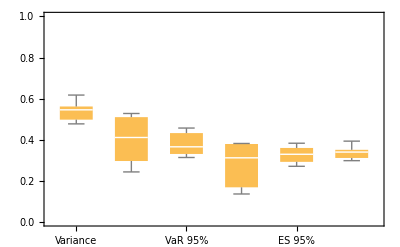

```mathematica
BoxWhiskerChart[heInsampleᵀ, ChartLabels->methods, PlotRange->{0,1}]
```

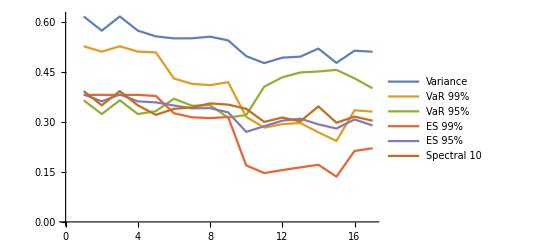

```mathematica
ListPlot[heInsampleᵀ,Joined->True, PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

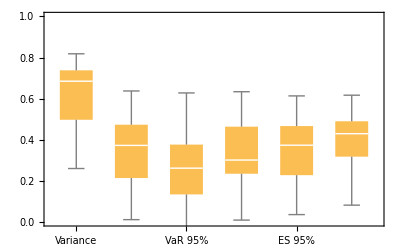

```mathematica
BoxWhiskerChart[heOutsampleᵀ, ChartLabels->methods, PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

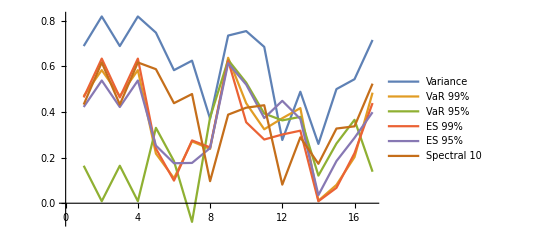

```mathematica
ListPlot[heOutsampleᵀ,Joined->True, PlotLegends->methods]
```

## P&L

### In-sample P&L

```mathematica
For[kk=1, kk≤14, kk++,
data = 
Import[NotebookDirectory[] <> "../processed_data/future_brr_v4/train/" <> ToString[kk] <> ".csv"];
btc=Reverse[data[[2;;,5]]];
brr = Reverse[data[[2;;,6]]];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={};
PLr={}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec⟦1;;-2⟧],jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

### Out-of-sample P&L

```mathematica
For[kk=1, kk≤14, kk++,
data = 
Import[NotebookDirectory[] <> "../processed_data/future_brr_v4/test/" <> ToString[kk] <> ".csv"];
btc=Reverse[data[[2;;,5]]];
brr = Reverse[data[[2;;,6]]];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={};
PLr={}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec[[;;-2]]],jj++,
h=hvec[[jj,1]];
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods[[jj]]];
AppendTo[PL, PLh];
PrependTo[rh, methods[[jj]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=1, kk≤14, kk++,
data = 
Import[NotebookDirectory[] <> "../processed_data/future_brr_v4/train/" <> ToString[kk] <> ".csv"];
btc=Reverse[data[[2;;,5]]];
brr = Reverse[data[[2;;,6]]];
hvec = Range[0.5, 1.5, 0.1];
PL={};
PLr={}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec],jj++,
h=hvec[[jj]];
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=1, kk≤14, kk++,
data = 
Import[NotebookDirectory[] <> "../processed_data/future_brr_v4/test/" <> ToString[kk] <> ".csv"];
btc=Reverse[data[[2;;,5]]];
brr = Reverse[data[[2;;,6]]];
hvec = Range[0.5, 1.5, 0.1];
PL={};
PLr={}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec],jj++,
h=hvec[[jj]];
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=1, kk≤14, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==1,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

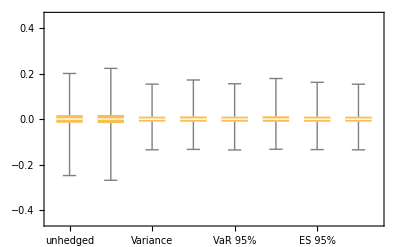

```mathematica
BoxWhiskerChart[d[[2;;]]ᵀ, ChartLabels->d[[1]],PlotRange->{Automatic, {-0.45, 0.45}}]
```

```mathematica
Dimensions[d]
```

{4201,7}

The overlap is clearly visible below.

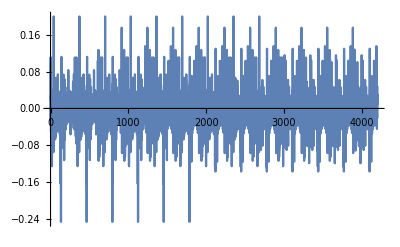

```mathematica
ListPlot[d[[2;;,1]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=1, kk≤14, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==1,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

```mathematica
Export[NotebookDirectory[] <> "data/" <> "PLr_outsample.csv",d];
```

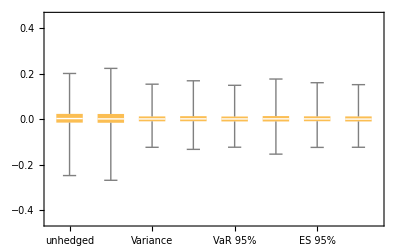

```mathematica
BoxWhiskerChart[d[[2;;]]ᵀ, ChartLabels->d[[1]],PlotRange->{Automatic, {-0.45, 0.45}}]
```

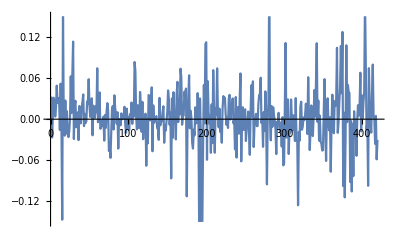
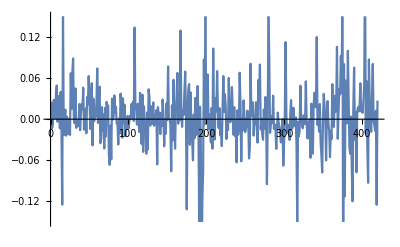

```mathematica
Table[ListPlot[d[[2;;,m]]ᵀ, Joined->True, PlotRange->{-0.15, 0.15}], {m,1,2}]
```

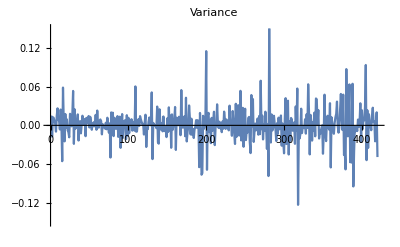
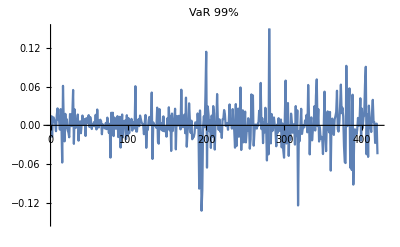
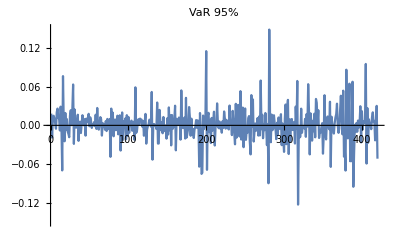
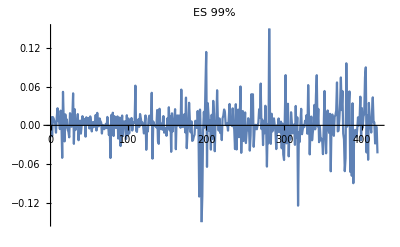
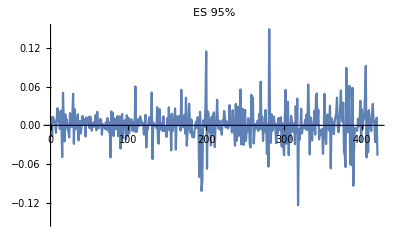
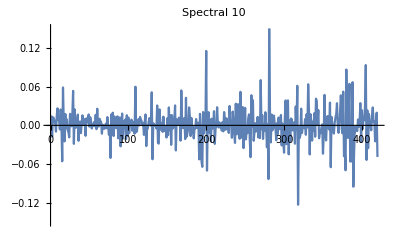

```mathematica
Table[ListPlot[d[[2;;,m]]ᵀ, Joined->True,PlotRange->{-0.15,0.15},PlotLabel->methods[[m-2]]], {m,3,8}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=1, kk≤14, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==1,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

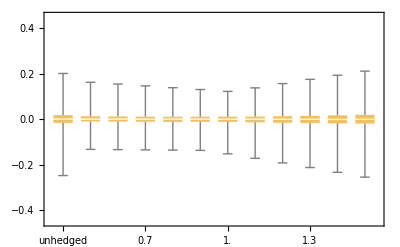

```mathematica
BoxWhiskerChart[d[[2;;]]ᵀ, ChartLabels->d[[1]],PlotRange->{Automatic, {-0.45, 0.45}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=1, kk≤14, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==1,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

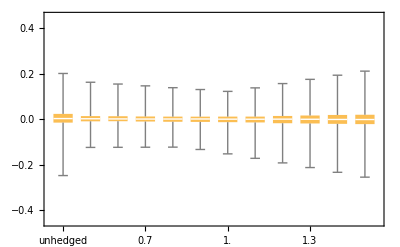

```mathematica
BoxWhiskerChart[d[[2;;]]ᵀ, ChartLabels->d[[1]],PlotRange->{Automatic, {-0.45, 0.45}}]
```

h time series

```mathematica
h={methods};
For[kk=1, kk≤14, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
h
```

(Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
0.703233 | 0.685991 | 0.588648 | 0.745188 | 0.754591 | 0.702218
0.7011 | 0.679456 | 0.647842 | 0.748339 | 0.727416 | 0.663945
0.668841 | 0.659297 | 0.775649 | 0.596866 | 0.696667 | 0.608827
0.666523 | 0.641972 | 0.764076 | 0.581348 | 0.673336 | 0.698125
0.665513 | 0.639025 | 0.76666 | 0.579193 | 0.649656 | 0.693044
0.663467 | 0.598779 | 0.712503 | 0.580866 | 0.611411 | 0.72356
0.61826 | 0.404323 | 0.623357 | 0.327333 | 0.520579 | 0.697891
0.604689 | 0.375528 | 0.583614 | 0.290648 | 0.503256 | 0.66834
0.614057 | 0.372819 | 0.636837 | 0.301453 | 0.514821 | 0.685477
0.607465 | 0.418027 | 0.669212 | 0.318843 | 0.525845 | 0.633373
0.626156 | 0.384379 | 0.712002 | 0.307701 | 0.513401 | 0.656942
0.598355 | 0.340534 | 0.642144 | 0.285822 | 0.523281 | 0.616036
0.64967 | 0.491233 | 0.679466 | 0.36855 | 0.590642 | 0.672447
0.658087 | 0.507627 | 0.745496 | 0.459958 | 0.585633 | 0.65286)

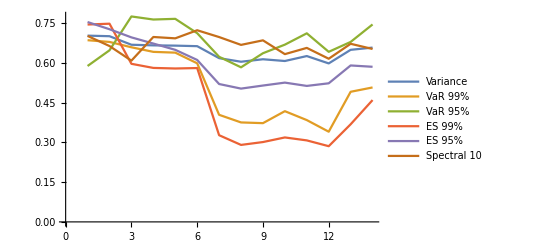

```mathematica
ListPlot[h[[2;;]]ᵀ,Joined->True,PlotLegends->h[[1]]]
```